# AD_Excitation

## 1D ground state

## useful function

```mathematica
colors = { RGBColor[162/255,37/255,143/255],RGBColor[25/255,169/255,172/255],Orange};Load energy[file_]:=ToExpression[StringReplace[StringSplit[ReadString[file]],"e"->"*10^"]][[-2]]
Load Time Step Energy gnorm[file_]:=ToExpression[StringReplace[StringSplit[ReadString[file]],"e"->"*10^"]]
```

## Heisenberg

#### relative error-χ

error exponentially-dependent on χ

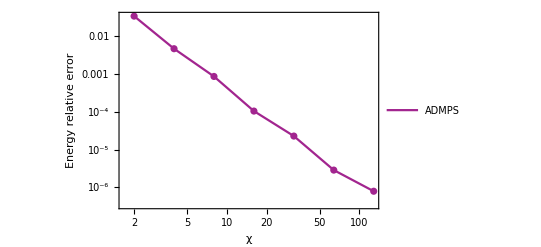

```mathematica
exact=0.25-Log[2];
AD MPS energy=Table[{2^i,Load energy["E:\\1 - research\\4.11 - Excitation_iPEPS\\AD_Excitation\\data\\Heisenberg{Float64}(0.5, 1.0, 1.0, 1.0)\\D2_χ"<>ToString[2^i]<>".log"]},{i,1,7}];
AD MPS energy aberror=Table[{AD MPS energy[[i,1]],Abs[(exact-AD MPS energy[[i,2]])/exact]},{i,1,Length[AD MPS energy]}];
ListLogLogPlot[{AD MPS energy aberror},PlotTheme->"Scientific",Mesh->All,Joined->True,PlotRange->All,PlotStyle->{colors [[1]],colors [[2]],colors [[3]],Blue},PlotLegends->Placed[{"ADMPS"},{Scaled[{0.7,0.8}], {0, 0}}],Joined->{True,True},Mesh->All,PlotTheme->"Scientific",FrameLabel->{{"Energy relative error",None},{HoldForm["χ"],None}},ImageSize->400]
```

#### relative error-steps

error exponentially-dependent on steps

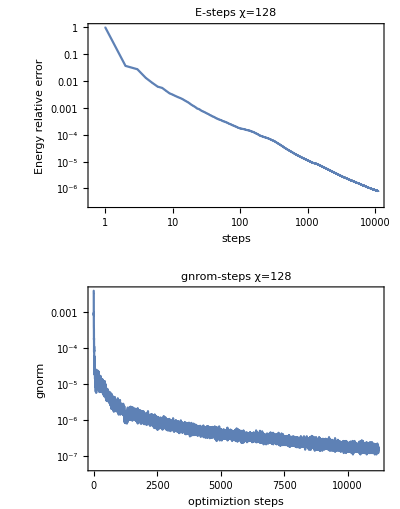

```mathematica
data=Load Time Step Energy gnorm["E:\\1 - research\\4.11 - Excitation_iPEPS\\AD_Excitation\\data\\Heisenberg{Float64}(0.5, 1.0, 1.0, 1.0)\\D2_χ128.log"];GraphicsGrid[{{ListLogLogPlot[Table[{i,Abs[(data[[4(i-1)+3]]-exact)/exact]},{i,1,Length[data]/4}],Joined->True,Mesh->All,PlotTheme->"Detailed",FrameLabel->{{HoldForm["Energy relative error"],None},{HoldForm["steps"],None}},PlotLabel->HoldForm["E-steps χ=128"],LabelStyle->{GrayLevel[0]},PlotRange->All]},{ListLogPlot[Table[{i,data[[4(i-1)+4]]},{i,1,Length[data]/4}],Joined->True,Mesh->All,PlotTheme->"Detailed",FrameLabel->{{HoldForm["gnorm"],None},{HoldForm["optimiztion steps"],None}},PlotRange->All,PlotLabel->HoldForm["gnrom-steps χ=128"]]}},ImageSize->400]
```

## TFIsing at critical point g=0.5

#### relative error-χ

error exponentially-dependent on χ

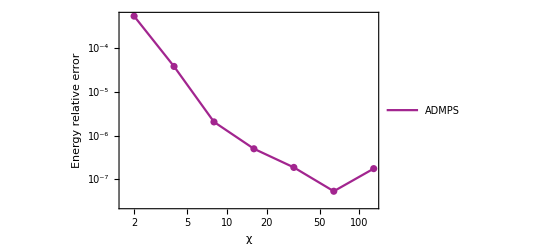

{{2,0.000547469},{4,0.0000384942},{8,2.06229×10^-6},{16,4.99614×10^-7},{32,1.86865×10^-7},{64,5.3171×10^-8},{128,1.75275×10^-7}}

```mathematica
g=1;exact=Integrate[-1/(2Pi)Sqrt[g^2-2g Cos[k]+1],{k,0,2Pi}]/4;
AD MPS energy=Table[{2^i,Load energy["E:\\1 - research\\4.11 - Excitation_iPEPS\\AD_Excitation\\data\\TFIsing{Float64}(0.5, 0.5)\\D2_χ"<>ToString[2^i]<>".log"]},{i,1,7}];
AD MPS energy aberror=Table[{AD MPS energy[[i,1]],Abs[(exact-AD MPS energy[[i,2]])/exact]},{i,1,Length[AD MPS energy]}];
ListLogLogPlot[{AD MPS energy aberror},PlotTheme->"Scientific",Mesh->All,Joined->True,PlotRange->All,PlotStyle->{colors [[1]],colors [[2]],colors [[3]],Blue},PlotLegends->Placed[{"ADMPS"},{Scaled[{0.7,0.8}], {0, 0}}],Joined->{True,True},Mesh->All,PlotTheme->"Scientific",FrameLabel->{{"Energy relative error",None},{HoldForm["χ"],None}},ImageSize->400]
AD MPS energy aberror
```

#### relative error-steps

error exponentially-dependent on steps

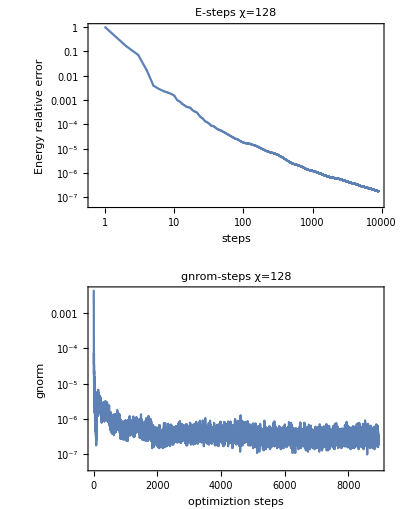

```mathematica
data=Load Time Step Energy gnorm["E:\\1 - research\\4.11 - Excitation_iPEPS\\AD_Excitation\\data\\TFIsing{Float64}(0.5, 0.5)\\D2_χ128.log"];GraphicsGrid[{{ListLogLogPlot[Table[{i,Abs[(data[[4(i-1)+3]]-exact)/exact]},{i,1,Length[data]/4}],Joined->True,Mesh->All,PlotTheme->"Detailed",FrameLabel->{{HoldForm["Energy relative error"],None},{HoldForm["steps"],None}},PlotLabel->HoldForm["E-steps χ=128"],LabelStyle->{GrayLevel[0]},PlotRange->All]},{ListLogPlot[Table[{i,data[[4(i-1)+4]]},{i,1,Length[data]/4}],Joined->True,Mesh->All,PlotTheme->"Detailed",FrameLabel->{{HoldForm["gnorm"],None},{HoldForm["optimiztion steps"],None}},PlotRange->All,PlotLabel->HoldForm["gnrom-steps χ=128"]]}},ImageSize->400]
```

## 1D Excitation

## U1

```mathematica
U1 = {{0.44214127746903376-0.36649815518214574I,-0.13700868205515632-0.16528649180042596I},{0.1370086836991797+0.1652864904376679I, 0.23346510468812767-0.1935230536660265I}};
U2 = {{Cos[x],-Sin[x]},{Sin[x],Cos[x]}}
```

{{Cos[x],-Sin[x]},{Sin[x],Cos[x]}}

```mathematica
FindRoot[Tr[Transpose[U1].U2]==0,{x,1}]
```

{x→1.5708+0.535137 ⅈ}

```mathematica
U=U2/.{x->1.5707963267948966+0.5351372028447591 ⅈ}
```

{{7.02112×10^-17-0.561047 ⅈ,-1.14664-3.43542×10^-17 ⅈ},{1.14664+3.43542×10^-17 ⅈ,7.02112×10^-17-0.561047 ⅈ}}

```mathematica
FullSimplify[Transpose[U].U]
```

{{1.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,1.+0. ⅈ}}

```mathematica
ConjugateTranspose[U]
```

{{7.02112×10^-17+0.561047 ⅈ,1.14664-3.43542×10^-17 ⅈ},{-1.14664+3.43542×10^-17 ⅈ,7.02112×10^-17+0.561047 ⅈ}}

## XXZ Δ=1

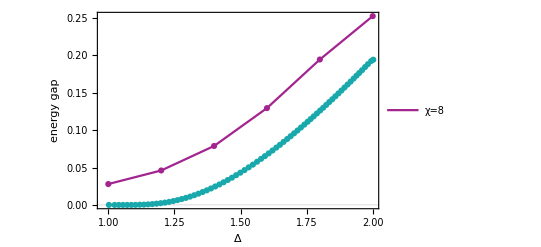

```mathematica
gap={0.05582453026702144,0.09212963838012368,0.15765165546585008,0.25902554676265305,0.38907021917034657,0.5051298373530196}/2;
energy gs=Table[{1.0+0.2(i-1),Load energy["E:\\1 - research\\4.11 - Excitation_iPEPS\\AD_Excitation\\data\\XXZ{Float64}("<>ToString[NumberForm[1.0+0.2(i-1),{2,1}]]<>")\\D2_χ8.log"]},{i,1,6}];
energy gap=Table[{energy gs[[i,1]],gap[[i]]},{i,1,Length[gap]}];
Exact = Import["E:\\1 - research\\4.11 - Excitation_iPEPS\\AD_Excitation\\project\\XXZ_gap.csv"];
ListPlot[{energy gap,Exact },PlotTheme->"Scientific",Mesh->All,Joined->True,PlotRange->All,PlotStyle->{colors [[1]],colors [[2]],colors [[3]],Blue},PlotLegends->Placed[{"χ=8"},{Scaled[{0.7,0.8}], {0, 0}}],Joined->{True,True},Mesh->All,PlotTheme->"Scientific",FrameLabel->{{"energy gap",None},{"Δ",None}},ImageSize->400]
```

## Heisenberg S=1/2

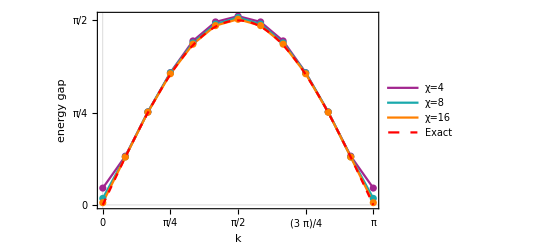

```mathematica
gap={{0.143590951236512,0.41530630963142906,0.7919144836295847,1.1263906176088896,1.3962166412387695,1.5578014262286415,1.6073219940962598,1.5578014252762273,1.3962166412329813,1.1263906186752397,0.791914483411365,0.415306313325118,0.14359095621658013},{0.055825535280367065,0.40920812813787655,0.7917343968681471,1.124766271557226,1.379519702559978,1.5398361831063736,1.5948824096077312,1.5398361216280303,1.3795198076975546,1.1247663680286026,0.791734354199969,0.40920812220705727,0.055826048730513896},{0.019355656610179933,0.40749600807271985,0.7893265909061853,1.116831940068277,1.368569477493216,1.526614821143771,1.5805417601476666,1.5266152002333788,1.3685691333818455,1.116831994201616,0.7893267774108071,0.40749554338175925,0.01936395160433102}};
gap=Table[{Pi/12 (i-1),gap[[j]][[i]]},{j,1,3},{i,1,Length[gap[[1]]]}];
Show[ListPlot[gap,PlotTheme->"Scientific",Mesh->All,Joined->True,PlotRange->All,PlotStyle->{colors [[1]],colors [[2]],colors [[3]],Blue},PlotLegends->Placed[{"χ=4","χ=8","χ=16"},{Scaled[{0.7,0.2}], {0, 0}}],Joined->{True,True},Mesh->All,PlotTheme->"Scientific",FrameTicks->{{{0,Pi/4,Pi/2,3Pi/4,Pi},Automatic},{{0,Pi/4,Pi/2,3Pi/4,Pi},Automatic}},FrameLabel->{{"energy gap",None},{"k",None}},LabelStyle->{FontFamily->"Times",24,GrayLevel[0]},ImageSize->400],Plot[Pi/2Sin[x],{x,0,Pi},PlotLegends->Placed[{"Exact"},{Scaled[{0.6,0.8}], {0, 0}}],PlotStyle->{Dashed,Red},LabelStyle->{FontFamily->"Times",24,GrayLevel[0]}]]
```

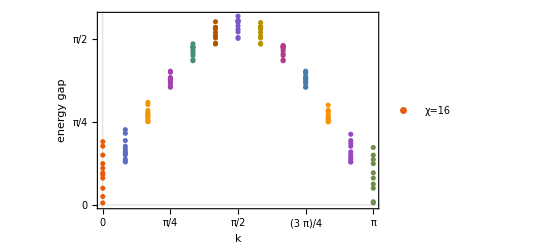

```mathematica
data={{0.019355656610179933,0.07988762037494206,0.1585253879374799,0.2546175161819573,0.28722951539495595,0.3045929369537908,0.34796944293680365,0.39224836756979004,0.4731106757708842,0.5577948606465597,0.6004863633592251,},{0.40749600807271985,0.4142521919225774,0.4335655929596041,0.4754024457333309,0.4928798807868131,0.5028107012652451,0.5287766185494969,0.5571479914894566,0.6106690243868612,0.6803876916185223,0.7141973112046429,},{0.7893265909061853,0.7942504809231549,0.8081007245040622,0.832984093539182,0.8371188242858568,0.8485807217577526,0.8607321151218807,0.8770475256075779,0.8965882339501734,0.9529234289970107,0.9734711299795026,},{1.116831940068277,1.1247658603647475,1.1543064373381107,1.1688018309748929,1.1799054875413757,1.193704799480487,1.2010722436078132,1.2011450778910417,1.2092200718925443,1.2590556683180554,1.269601453564205,},{1.368569477493216,1.37675229199881,1.4175154809806227,1.443541654448123,1.4655694754670185,1.4894502711154745,1.4964225299111504,1.4989460475681284,1.500578951953526,1.5290848624191908,},{1.526614821143771,1.535150428349417,1.585207105311804,1.6093701824411302,1.6364887648388071,1.668185901366304,1.6823606800559647,1.6844606823311228,1.6847366315895733,1.7385843558977334,},{1.5805417601476666,1.5886596446707208,1.6417548362212293,1.6655559098640553,1.6991849478621377,1.7327549153320576,1.7433851023055071,1.7497370113579613,1.7512432583535884,1.791863652717134,},{1.5266152002333788,1.5337563972902744,1.5852060636819754,1.603846391111866,1.6364882796188933,1.6681973702599486,1.682404249880471,1.68442145864912,1.6930124803431266,1.7304374452243074,},{1.3685691333818455,1.3740025943305194,1.4175184058984587,1.4341914477244695,1.4655656347228228,1.4894594422290999,1.4964402584038157,1.500556539026063,1.5065255724745015,1.513519076021784,},{1.116831994201616,1.1207258193087406,1.1543069871817087,1.1607399569130774,1.1799058344800217,1.193711719000192,1.2011541471664386,1.2092081130749324,1.2153521181888893,1.2467177105954983,1.257492645709368,1.2694960550746015,},{0.7893267774108071,0.7913374714945234,0.8081013145244947,0.815414193242881,0.8329836339265184,0.8486172394258708,0.8770336181260813,0.8917946696014732,0.8965996244967185,0.9466788488111871,},{0.40749554338175925,0.40832852386517876,0.4335704969061045,0.44972908744185897,0.475401525096523,0.5028876060395602,0.5571424014911442,0.5838977691304374,0.6106743524522784,0.670819454663252,},{0.01936395160433102,0.029915782692426826,0.15854506940212898,0.19815166388841593,0.2546175202379102,0.30474020170825267,0.3922532691849,0.4313049430777801,0.47310815456613925,0.5454350734939086,}};
energy gap=Table[Transpose@{Table[Pi/12 (i-1),{j,1,Length[data[[i]]]}],data[[i]]},{i,1,Length[data]}];
Show[ListPlot[energy gap,PlotTheme->"Scientific",Mesh->All,Joined->False,PlotRange->All,PlotStyle->{},Mesh->All,PlotTheme->"Scientific",FrameLabel->{{"energy gap",None},{"k",None}},PlotLegends->Placed[{"χ=16"},{Scaled[{0.5,0.2}], {0, 0}}],FrameTicks->{{{0,Pi/4,Pi/2,3Pi/4,Pi},Automatic},{{0,Pi/4,Pi/2,3Pi/4,Pi},Automatic}},LabelStyle->{FontFamily->"Times",24,GrayLevel[0]},ImageSize->400]]
```

## Heisenberg S=1

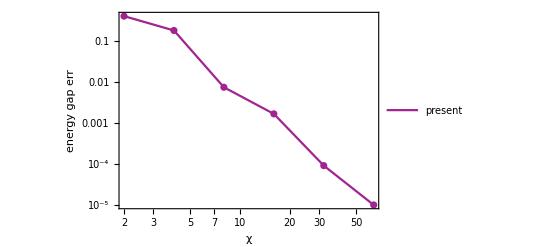

```mathematica
gap={0.5811172937623585,0.4864179655123887,0.40739832778964274,0.40979313525841843,0.41044228122259074,0.410475228123841};
Verstraete2012=0.410479248463;
energy gap=Table[{2^i,Abs[(gap[[i]]-Verstraete2012)/Verstraete2012]},{i,1,Length[gap]}];
Show[ListLogLogPlot[{energy gap},PlotTheme->"Scientific",Mesh->All,Joined->True,PlotRange->All,PlotStyle->{colors [[1]],colors [[2]],colors [[3]],Blue},PlotLegends->Placed[{"present","Verstraete2012"},{Scaled[{0.6,0.5}], {0, 0}}],Joined->{True,True},Mesh->All,PlotTheme->"Scientific",FrameLabel->{{"energy gap err",None},{"χ",None}},LabelStyle->{FontFamily->"Times",24,GrayLevel[0]},ImageSize->400],PlotRange->All]
```